```mathematica
(*Created at Mar 25,2017 by qz2280@columbia.edu*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
v[eta_,{i_,j_}]:=Switch[eta,0,{i,j},1,{i,j-1},2,{i-1,j}]
w[eta_,{i_,j_}]:=Switch[eta,0,{i+1,j},1,{i+1,j-1},2,{i,j+1}]
```

```mathematica
V1[i_,j_]:=1/2 gammaSigma Sum[(-Cos[2Pi/3 eta]u[{i,j},{A,x}]-Sin[2Pi/3 eta]u[{i,j},{A,y}]+Cos[2Pi/3 eta]u[v[eta,{i,j}],{B,x}]+Sin[2Pi/3 eta]u[v[eta,{i,j}],{B,y}])^2,{eta,0,2,1}]/.{gammaSigma->27.3};
V2[i_,j_]:=1/2 gammaPi Sum[(Sin[2Pi/3 eta]u[{i,j},{A,x}]-Cos[2Pi/3 eta]u[{i,j},{A,y}]-Sin[2Pi/3 eta]u[v[eta,{i,j}],{B,x}]+Cos[2Pi/3 eta]u[v[eta,{i,j}],{B,y}])^2,{eta,0,2,1}]/.{gammaPi->10.205};
V3[i_,j_]:=1/2 gammaSigmaPrime Sum[(-Cos[Pi/3 eta+Pi/6] u[{i,j},{alpha,x}]-Sin[Pi/3 eta+Pi/6] u[{i,j},{alpha,y}]+Cos[Pi/3 eta+Pi/6] u[w[eta,{i,j}],{alpha,x}]+Sin[Pi/3 eta+Pi/6] u[w[eta,{i,j}],{alpha,y}])^2,{alpha,{A,B}},{eta,0,2,1}]/.{gammaSigmaPrime->4.69};
V4[i_,j_]:=1/2 gammaPiPrime Sum[(Sin[Pi/3 eta+Pi/6] u[{i,j},{alpha,x}]-Cos[Pi/3 eta+Pi/6] u[{i,j},{alpha,y}]-Sin[Pi/3 eta+Pi/6] u[w[eta,{i,j}],{alpha,x}]+Cos[Pi/3 eta+Pi/6] u[w[eta,{i,j}],{alpha,y}])^2,{alpha,{A,B}},{eta,0,2,1}]/.{gammaPiPrime->-2.615};
```

```mathematica
VTotal=Sum[V1[i,j]+V2[i,j],{i,-1,2},{j,-1,2}]+Sum[V3[i,j]+V4[i,j],{i,-2,2},{j,-2,2}];
```

```mathematica
Phi[i_,j_]:=Table[D[D[VTotal,u[{0,0},m]],u[{i,j},n]],{m,{{A,x},{A,y},{B,x},{B,y}}},{n,{{A,x},{A,y},{B,x},{B,y}}}]
```

```mathematica
dynamicalMatrix[k1_,k2_]:=Sum[Exp[2 Pi I (k1 i+k2 j)] Phi[i,j],{i,-1,1},{j,-1,1}]
massMatrix=DiagonalMatrix[{carbonMass+epsilon,carbonMass+epsilon,carbonMass-epsilon,carbonMass-epsilon}];
eigval[k1_,k2_]:=Eigenvalues[{dynamicalMatrix[k1,k2],massMatrix}]
scalingFactor=Sqrt[1/(6.2415*10^-2)]*6.582*10^-16*8065.6;
omega[k1_,k2_]:=(eig=eigval[k1,k2];
Sign[eig]*Sqrt[Abs[eig]]*scalingFactor)
```

```mathematica
(*Plot3D[omega[k1,k2],{k1,0,1},{k2,0,1}]*)
```

```mathematica
gm:=Plot[omega[k,k],{k,0,1/2},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRangePadding->{{None,None},{1,1}},AspectRatio->Sqrt[2],PlotRange->{0,2000}](*Gamma->M path*)
```

```mathematica
mk:=Plot[omega[k,1-k]//Sort,{k,1/2,2/3},Frame->True,PlotRangePadding->{{None,None},{1,1}},AspectRatio->6/Sqrt[2],PlotRange->{0,2000}](*M->K path*)
```

```mathematica
kg:=Plot[omega[k,1/2k],{k,2/3,0},ScalingFunctions->{"Reverse",Identity}(*Invert horizontal axis*),Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->{{None,None},{1,1}},AspectRatio->3/Sqrt[5],PlotRange->{0,2000}](*K->Gamma path*)
```

```mathematica
(*Below is combine plots function,do not change this.*)
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
carbonMass=12.011*1.66054*10^-27;epsilon=carbonMass/n;
```

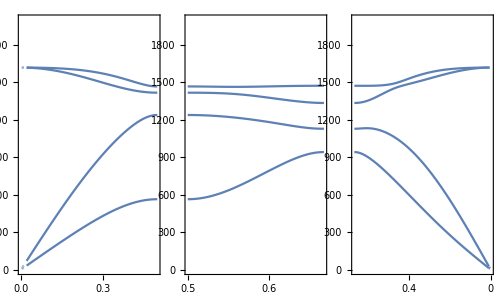
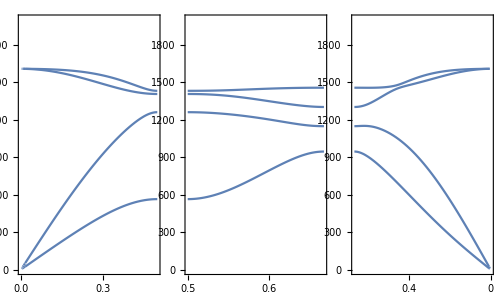
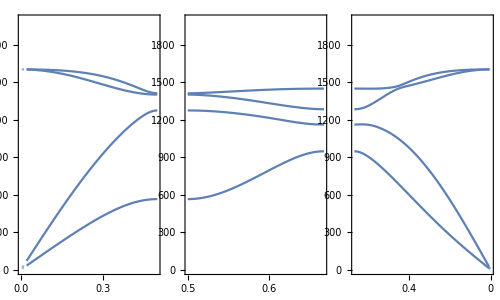
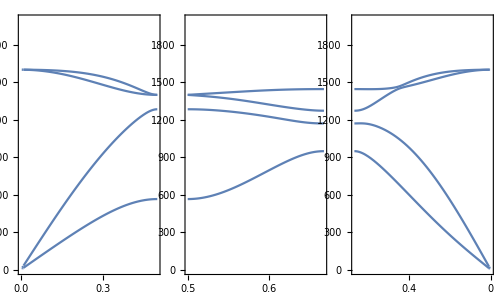

```mathematica
Table[plotGrid[{{gm,mk,kg}},500,300,ImagePadding->30],{n,{6,8,10,12}}]
```

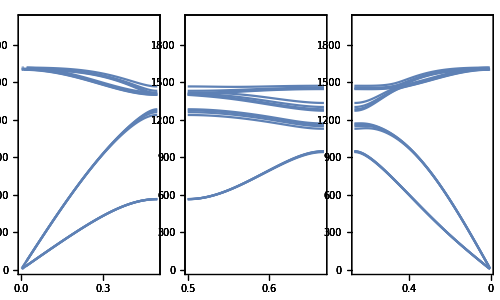

```mathematica
Show[%]
```